ref: “Practical Applications of Bayesian Reliability”

#### sample using reliability function

```mathematica
Clear["Global`*"];
SeedRandom[0];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

```mathematica
data=Import["~/Downloads/Computer_scripts_and_data_files/Example8.2Data_ttf_Table8.4.txt","TSV"][[2;;,2;;]];
cenlim=Import["~/Downloads/Computer_scripts_and_data_files/Example8.2Data_CenLimit_Table8.5.txt","TSV"][[2;;,2;;]];
censor=Import["~/Downloads/Computer_scripts_and_data_files/Example8.2Data_CensorLG_Table8.6.txt","TSV"][[2;;,2;;]];
censor=Table[Table[If[censor[[i,j]]=="FALSE",False,True],{j,10}],{i,100}];
data1=Table[Table[If[data[[i,j]]=="NA",cenlim[[i,j]],data[[i,j]]],{j,10}],{i,100}];
```

```mathematica
(*trueShape={1.05271,1.30417,1.25654,1.53451,1.58226,1.33131,1.38997,2.15500,1.47402,1.28420};
trueScale={681.011,610.300,489.721,439.992,570.550,549.467,674.867,510.555,610.915,667.784};
cenlim=Import["~/Downloads/Computer_scripts_and_data_files/Example8.2Data_CenLimit_Table8.5.txt","TSV"][[2;;,2;;]];
censor=Table[False,100,10];
data1=Table[0,100,10];
Do[Do[v=RandomVariate[WeibullDistribution[trueShape[[j]],trueScale[[j]]]];chmc-mcmcIf[v>cenlim[[i,j]],censor[[i,j]]=True;data1[[i,j]]=cenlim[[i,j]],data1[[i,j]]=v],{j,1,10}],{i,1,100}]*)
```

```mathematica
Α={α1,α2,α3,α4,α5,α6,α7,α8,α9,α10};
Β={β1,β2,β3,β4,β5,β6,β7,β8,β9,β10};
```

```mathematica
U0[α1_,α2_,α3_,α4_,α5_,α6_,α7_,α8_,α9_,α10_,β1_,β2_,β3_,β4_,β5_,β6_,β7_,β8_,β9_,β10_,a_,b_,c_,d_]=Simplify[Sum[Sum[PowerExpand[-Log[Simplify[If[censor[[i,j]],1-CDF[WeibullDistribution[α,β],y],PDF[WeibullDistribution[α,β],y]],y>0]]]/.{y->data1[[i,j]],α->Α[[j]],β->Β[[j]]},{i,1,100}],{j,1,10}]+Sum[(PowerExpand[-Log[Simplify[PDF[GammaDistribution[a,b1],α],α>0]]]+PowerExpand[-Log[Simplify[PDF[GammaDistribution[c,d1],β],β>0]]])/.{b1->1/b,d1->1/d,α->Α[[j]],β->Β[[j]]},{j,1,10}]];
```

```mathematica
mle=Table[Last[FindMinimum[{U0[α1,α2,α3,α4,α5,α6,α7,α8,α9,α10,β1,β2,β3,β4,β5,β6,β7,β8,β9,β10,a,b,c,d],α1>0&&α2>0&&α3>0&&α4>0&&α5>0&&α6>0&&α7>0&&α8>0&&α9>0&&α10>0&&α1<3&&α2<3&&α3<3&&α4<3&&α5<3&&α6<3&&α7<3&&α8<3&&α9<3&&α10<3&&β1>0&&β2>0&&β3>0&&β4>0&&β5>0&&β6>0&&β7>0&&β8>0&&β9>0&&β10>0&&β1<1000&&β2<1000&&β3<1000&&β4<1000&&β5<1000&&β6<1000&&β7<1000&&β8<1000&&β9<1000&&β10<1000&&a>0&&b>0&&c>0&&d>0&&a<90-10ii&&b<90-10ii&&c<90- 10ii&&d<90-10ii},{α1,α2,α3,α4,α5,α6,α7,α8,α9,α10,β1,β2,β3,β4,β5,β6,β7,β8,β9,β10,a,b,c,d}]],{ii,1,CHAINS}];
```

```mathematica
qinit=Table[{α1,α2,α3,α4,α5,α6,α7,α8,α9,α10,β1,β2,β3,β4,β5,β6,β7,β8,β9,β10,a,b,c,d}/.mle[[ii]],{ii,1,CHAINS}];
```

```mathematica
outbnd[q_]:=AnyTrue[q[[1;;20]],#<=0.0&]||AnyTrue[q[[21;;24]],(#<=0.0||#≥100)&];
```

```mathematica
U[α1_,α2_,α3_,α4_,α5_,α6_,α7_,α8_,α9_,α10_,β1_,β2_,β3_,β4_,β5_,β6_,β7_,β8_,β9_,β10_,a_,b_,c_,d_]=U0[α1,α2,α3,α4,α5,α6,α7,α8,α9,α10,β1,β2,β3,β4,β5,β6,β7,β8,β9,β10,a,b,c,d];
```

```mathematica
dU[α1_,α2_,α3_,α4_,α5_,α6_,α7_,α8_,α9_,α10_,β1_,β2_,β3_,β4_,β5_,β6_,β7_,β8_,β9_,β10_,a_,b_,c_,d_]=Simplify[GradientG[U[α1,α2,α3,α4,α5,α6,α7,α8,α9,α10,β1,β2,β3,β4,β5,β6,β7,β8,β9,β10,a,b,c,d],{α1,α2,α3,α4,α5,α6,α7,α8,α9,α10,β1,β2,β3,β4,β5,β6,β7,β8,β9,β10,a,b,c,d}]];
ddU[α1_,α2_,α3_,α4_,α5_,α6_,α7_,α8_,α9_,α10_,β1_,β2_,β3_,β4_,β5_,β6_,β7_,β8_,β9_,β10_,a_,b_,c_,d_]=Simplify[HessianH[U[α1,α2,α3,α4,α5,α6,α7,α8,α9,α10,β1,β2,β3,β4,β5,β6,β7,β8,β9,β10,a,b,c,d],{α1,α2,α3,α4,α5,α6,α7,α8,α9,α10,β1,β2,β3,β4,β5,β6,β7,β8,β9,β10,a,b,c,d}]];
```

```mathematica
INTERVAL=1001;

QS=hmc[U,dU,ddU,24,20000,50000,True,True,qinit];
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{79.4806,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0500464,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.758975,1.,0.,0.},«22»,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,-67.659,31802.3}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{79.3854,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0500037,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.758915,1.,0.,0.},«22»,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,-67.413,31671.2}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

```mathematica
QQ=Table[QS[[i;;Length[QS];;CHAINS,;;]],{i,1,CHAINS}];
```

```mathematica
Table[ListPlot[Table[QQ[[i,;;,j]],{i,CHAINS}],PlotStyle->Opacity[.1]],{j,24}]
```

```mathematica
Table[j,{j,21,24}]
```

{21,22,23,24}

```mathematica
GraphicsGrid[
ArrayReshape[Table[ListPlot[Table[QQ[[i,;;,j]],{i,CHAINS}],PlotStyle->Opacity[.1],Ticks->{None,None}],{j,1,20,2}],{2,5}]]
```

```mathematica
GraphicsRow[Table[ListPlot[Table[QQ[[i,;;,j]],{i,CHAINS}],PlotStyle->Opacity[.1],Ticks->{None,None}],{j,21,24}]]
```

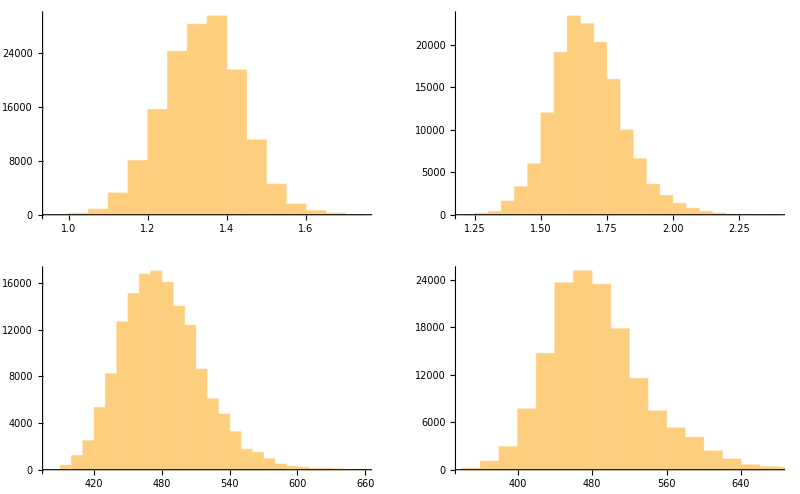

```mathematica
GraphicsGrid[ArrayReshape[Table[Histogram[QS[[;;,j]]],{j,1,20,5}],{2,2}]]
```

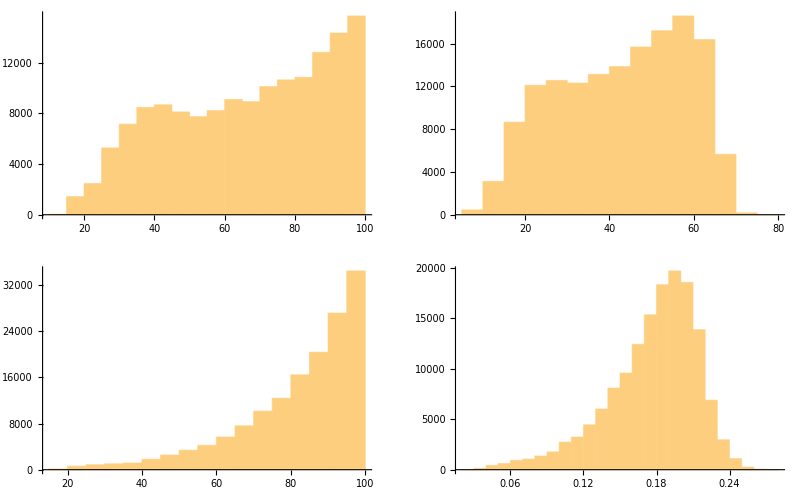

```mathematica
GraphicsGrid[ArrayReshape[Table[Histogram[QS[[;;,j]]],{j,21,24}],{2,2}]]
```

```mathematica
QS//Dimensions
```

{150000,24}

```mathematica
psrf1=psrf[QS]
```

{1.00051,1.00214,1.0027,1.01493,1.01123,1.00704,1.00547,1.00755,1.01973,1.00493,1.0023,1.00575,1.00475,1.01332,1.01575,1.00763,1.01481,1.00172,1.01068,1.00675,1.00995,1.01174,1.00069,1.00204}

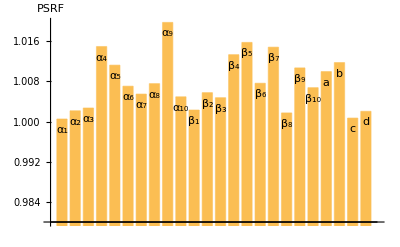

```mathematica
BarChart[psrf1,ChartLabels->Placed[{"α_1","α_2","α_3","α_4","α_5","α_6","α_7","α_8","α_9","α_10","β_1","β_2","β_3","β_4","β_5","β_6","β_7","β_8","β_9","β_10","a","b","c","d"},Top],PlotRange->{Automatic,{.98,Max[psrf1]}},AxesLabel->{None,"PSRF"}]
```

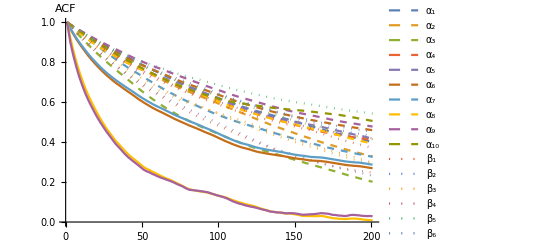

```mathematica
ListPlot[Table[CorrelationFunction[QQ[[1,;;,i]],{200}],{i,24}],(*Filling->Axis,*)PlotRange->All,Joined->True,AxesLabel->{None,"ACF"},PlotLegends->{Subscript[α, 1],Subscript[α, 2],Subscript[α, 3],Subscript[α, 4],Subscript[α, 5],Subscript[α, 6],Subscript[α, 7],Subscript[α, 8],Subscript[α, 9],Subscript[α, 10],Subscript[β, 1],Subscript[β, 2],Subscript[β, 3],Subscript[β, 4],Subscript[β, 5],Subscript[β, 6],Subscript[β, 7],Subscript[β, 8],Subscript[β, 9],Subscript[β, 10],a,b,c,d},PlotStyle->{Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dotted,Dotted,Dotted,Dotted,Dotted,Dotted,Dotted,Dotted,Dotted,Dotted,Dashing,Dashing,Dashing,Dashing}]
```

```mathematica
Export["hier_weilbuff2.csv",QS]
```

hier_weilbuff2.csv

```mathematica
QS=Import["/var/u1/share/hier_weilbuff2.csv"];
```

```mathematica
{StandardDeviation[reliability]}//Transpose//MatrixForm
```

(0.0147372
0.0133189
0.0136845
0.0108639
0.00876706
0.00917986
0.011838
0.00964276
0.0116887
0.0144135)

```mathematica
StandardDeviation[QS]
```

{0.0983943,0.104611,0.102389,0.123403,0.139816,0.135459,0.115443,0.15132,0.13728,0.1463,35.8692,37.9126,37.0321,40.3067,53.0107,53.7849,48.8826,61.2493,56.3561,53.2823,22.6447,15.1168,16.0177,0.0368763}

```mathematica
Quantile[reliability,{.025,.5,.975}]//MatrixForm
```

(0.873271 | 0.907308 | 0.931485
0.878688 | 0.908362 | 0.930832
0.867511 | 0.898339 | 0.921059
0.90361 | 0.927328 | 0.946231
0.930588 | 0.949886 | 0.965098
0.927381 | 0.947752 | 0.963909
0.899762 | 0.926156 | 0.945571
0.933453 | 0.953312 | 0.971395
0.916132 | 0.940643 | 0.962334
0.905447 | 0.937372 | 0.962732)

```mathematica
reliability//Dimensions
```

{150000,10}

```mathematica
QS//Dimensions
```

{}

```mathematica
reliability=Transpose[Table[Exp[-(84/QS[[;;,j+10]])^QS[[;;,j]]],{j,1,10}]];
```

```mathematica
Export["/var/u1/share/hier_weilbuff2_reliability2.csv",reliability]
```

/var/u1/share/hier_weilbuff2_reliability2.csv

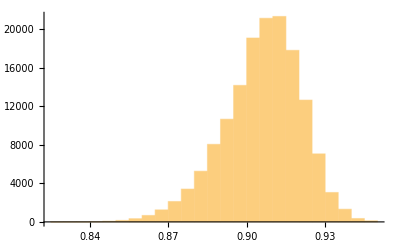
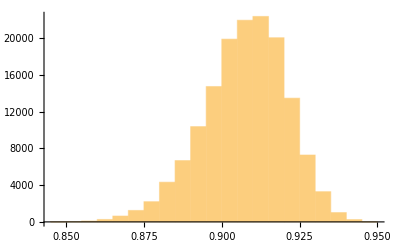
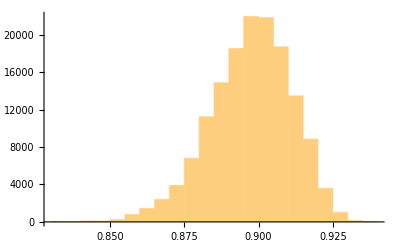
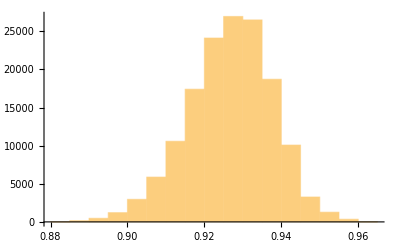
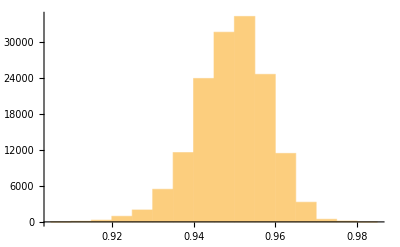
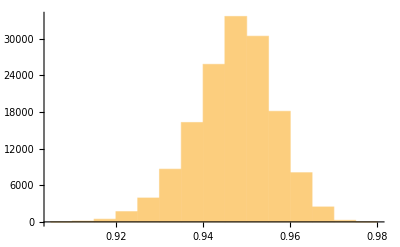
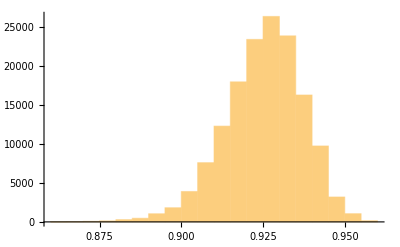
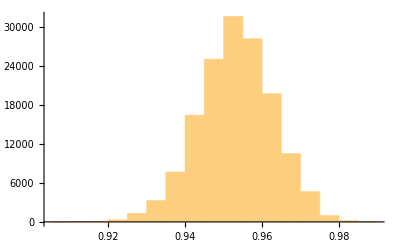

```mathematica
Table[Histogram[reliability[[;;,i]]],{i,1,10}]
```

```mathematica
Mean[reliability]
```

{0.905963,0.907385,0.897343,0.92666,0.949357,0.947175,0.925201,0.953178,0.940129,0.936504}

```mathematica
codaMatrix=Import["~/Downloads/Computer_scripts_and_data_files/codaMatrix83.csv"];
```

```mathematica
codaMatrix1=codaMatrix[[2;;,{5,6,7,8,9,10,11,12,13,14}]]
```

{{0.910255,0.916108,0.8896,0.959818,0.939089,0.944948,0.929218,0.967041,0.963186,0.966924},99998,{0.915121,0.900324,0.875742,4,0.966393,0.921948,0.923078}}
 |  |  |  |

```mathematica
Quantile[codaMatrix1,{0.025,0.5,0.975}]//MatrixForm
```

(0.858677 | 0.907308 | 0.940689
0.862917 | 0.908232 | 0.940926
0.849447 | 0.897288 | 0.932265
0.88989 | 0.928841 | 0.956932
0.923384 | 0.955497 | 0.977312
0.922005 | 0.955014 | 0.977699
0.888624 | 0.929881 | 0.95932
0.930719 | 0.96424 | 0.986794
0.909179 | 0.950619 | 0.978984
0.897682 | 0.949385 | 0.983985)

```mathematica
{StandardDeviation[codaMatrix1]}//Transpose//MatrixForm
```

(0.021021
0.019982
0.0212148
0.0171386
0.0137983
0.0142925
0.01808
0.0143825
0.0179786
0.0222068)